2

Arithmetic Principles

## 2.Section. You should know some rules about addition

The first arithmetic operation is addition. In Mathematica, it is simply called Plus.

```mathematica
Plus[1,3,4]
```

8

You may also think of it as a binary operator, meaning that it only takes two arguments:

```mathematica
Plus[1,1]
```

2

Showing this formulate in different form, we can demonstrate that Mathematica actually interprets this expression in an “infix” form, meaning that it uses the + sign in the middle of two arguments.

```mathematica
Hold[Plus[a,b,c,d]]
```

Hold[a+b+c+d]

The goal of this chapter is to learn to build an Arithmetic Logic Unit to perform integer adding functions. To learn to do this, we need to first understand how integer numbers are represented in various base forms.

## 2.Section. Integer Number Representation

Integer numbers can be represented in a decimal system, but it can also be written down in various other base forms. For example, if we represent the following numbers in base form of 8, then, we can show these numbers as follows:

```mathematica
numbers = Table[i,{i,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
BaseForm[numbers,8]
```

{1_8,2_8,3_8,4_8,5_8,6_8,7_8,10_8,11_8,12_8,13_8,14_8,15_8,16_8,17_8,20_8,21_8,22_8,23_8,24_8}

Similarly, we can show these numbers in the base form of 16, also known as hexadecimal form:

```mathematica
BaseForm[numbers,16]
```

{1_16,2_16,3_16,4_16,5_16,6_16,7_16,8_16,9_16,a_16,b_16,c_16,d_16,e_16,f_16,10_16,11_16,12_16,13_16,14_16}

In this chapter, we are going to represent these numbers in their binary form, therefore we can let the machine to do the translation:

```mathematica
BaseForm[numbers,2]
```

{1_2,10_2,11_2,100_2,101_2,110_2,111_2,1000_2,1001_2,1010_2,1011_2,1100_2,1101_2,1110_2,1111_2,10000_2,10001_2,10010_2,10011_2,10100_2}

### 2.Section.Subsection. Addition operation for different base forms follows the same rewrite rule

For numbers represented in any base forms, the rules to perform addition are the same. When the symbol set within the same digit cannot represent the added number, we take the remainder and write it down as the current digit, then, jot down the result of the “carry over” and add it to the digit on the immediate left side of the current digit. This rule can be applied recursively to any number.

```mathematica
first=290;
second=538;
numberOfDigits=4;
base=10;
denominations=Table[base^i,{i, 0,numberOfDigits-1}]//Reverse;
firstSet=NumberDecompose[first,denominations];
secondSet=NumberDecompose[second, denominations];
sumOfTwoSets=firstSet+secondSet;
sumOfTwoSets=Map[BaseForm[#,base]&,sumOfTwoSets]
finalDigits =Map[BaseForm[#,base]&,NumberDecompose[first + second, denominations]];
Grid[{firstSet, secondSet, sumOfTwoSets,finalDigits}, Spacings -> {2, 2}, Background -> {{None, None, None}, {None,None, LightGray, Gray}}]
BaseForm[(first + second),base]
```

{0,7,12,8}

0 | 2 | 9 | 0
0 | 5 | 3 | 8
0 | 7 | 12 | 8
0 | 8 | 2 | 8

828

To do this problem in binary form, we can add two numbers as the following:

```mathematica
first=7;
second=6;
numberOfDigits=5;
base=2;
denominations=Table[base^i,{i, 0,numberOfDigits-1}]//Reverse;
firstSet=NumberDecompose[first,denominations];
secondSet=NumberDecompose[second, denominations];
sumOfTwoSets=firstSet+secondSet;
sumOfTwoSets=Map[BaseForm[#,base]&,sumOfTwoSets]
finalDigits =Map[BaseForm[#,base]&,NumberDecompose[first + second, denominations]];
Grid[{firstSet, secondSet, sumOfTwoSets,finalDigits}, Spacings -> {2, 2}, Background -> {{None, None, None}, {None,None, LightGray, Gray}}]
BaseForm[(first + second),base]
```

{0_2,0_2,10_2,10_2,1_2}

0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0
0_2 | 0_2 | 10_2 | 10_2 | 1_2
0_2 | 1_2 | 1_2 | 0_2 | 1_2

1101_2

The readers are welcome to play with the paramters of the above program to test the digit-wise rewrite rules of addition arithmetic.

### 2.Section.Subsection. The substraction operation

In the video of TECS course, it was said that negative numbers are represented in a way so that it is easy to perform substraction by adding a negative number. Therefore this raise two questions. First, how is a negative number represetned in binary with regard to this TECS’s design contract. Second, how do we turn a regular positive number into a negative number.

The clever way as Noam Nisan mentioned in his talk, says that all negative numbers all have its 16th bit given the value of 1, and the values of the remaining bits are simply flipping the {1,0} values of the positive number’s bitwise representation. If this approach works, then, we solved both problems as stated earlier. First, we know how to represent a negative number, by having the most significant bit (MSB) to show the value of 1, and use a Not16 chip to flip all bits to its inverse values. Then, we just continue to use the Adder as it was originally implemented.  But is this true? Moreover, why would this be true?

### 2.Section.Subsection. Substraction by overflow

So, let’s study this number theoretical problem with Mathematica. To help everyone understand this approach, we may start with decimal number systems.

For example, if we want to substract 1 from a two digit system, say 35, we may just add 99 to 35, and get 134, then ignore the carry over value by 100. The remaining two digits would be identical to 35-1. This can be illustrated as follow:

```mathematica
first=8;
second=9;
numberOfDigits=4;
base=10;
denominations=Table[base^i,{i, 0,numberOfDigits-1}]//Reverse;
firstSet=NumberDecompose[first,denominations];
secondSet=NumberDecompose[second, denominations];
sumOfTwoSets=firstSet+secondSet;
sumOfTwoSets=Map[BaseForm[#,base]&,sumOfTwoSets]
finalDigits =Map[BaseForm[#,base]&,NumberDecompose[first + second, denominations]];
Grid[{firstSet, secondSet, sumOfTwoSets,finalDigits}, Spacings -> {2, 2}, Background -> {{None, None, None}, {None,None, LightGray, Gray}}]
BaseForm[(first + second),base]
```

{0,0,0,17}

0 | 0 | 0 | 8
0 | 0 | 0 | 9
0 | 0 | 0 | 17
0 | 0 | 1 | 7

17

If we just ignore the carry over value by 10, then the resulting value of 8-1 is equal to 7.

This property would also work with binary system. Therefore, by adding 31 to arbitrary positive numbers in a 5 digit binary system, the remaing four bits, will also be equal to the original number -1.

```mathematica
first=28;
second=31;
numberOfDigits=5;
base=2;
denominations=Table[base^i,{i, 0,numberOfDigits-1}]//Reverse;
firstSet=NumberDecompose[first,denominations];
secondSet=NumberDecompose[second, denominations];
sumOfTwoSets=firstSet+secondSet;
sumOfTwoSets=Map[BaseForm[#,base]&,sumOfTwoSets]
finalDigits =Map[BaseForm[#,base]&,NumberDecompose[first + second, denominations]];
Grid[{firstSet, secondSet, sumOfTwoSets,finalDigits}, Spacings -> {2, 2}, Background -> {{None, None, None}, {None,None, LightGray, Gray}}]
BaseForm[(first + second)-base^numberOfDigits,base]
BaseForm[(first + second)-base^numberOfDigits,10]
```

{10_2,10_2,10_2,1_2,1_2}

1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1
10_2 | 10_2 | 10_2 | 1_2 | 1_2
11_2 | 1_2 | 0_2 | 1_2 | 1_2

11011_2

27

We can see that if we want to substract 2 out of an existing value, we would simply add 30 which equals to 32-2 to the number, remove the carry over value, and get the result.

```mathematica
Manipulate[{first, BaseForm[first,2],BaseForm[32-first,2]},{first, 0,31,1}]
```

Following this thread of thoughts, we may infer the rule that a negative number in a limited digital represtation, can be implemented by creating a number that is the identical magnitude of the negative number. This can be accomplished by just using the 2’s complement.

## 2.3. Adders in digital circuits

Knowing that addition is simply a kind of rewrite rule, we can implement these rewrite rules by digital circuits, not by hand writing. The following section shows how one can do this in simple boolean logic.

### 2.3.1 Half Adder

An intuitive way to look at half adder is by looking at the possible binary values of each bit-wise input-output pair. A half adder is a bit-wise addition unit, that properly returns the {0,1} values according to value combinations of two input bits, {a,b}. The following truth table lists the values of all four pins, {a,b,carry and sum}.

```mathematica
Grid[Insert[BooleanTable[{a, b, And[a,b],Xor[a, b]}, {a,b}] // Boole, {a, b, carry, sum}, 1], Spacings -> {2, 1}, Frame -> All, Background -> {{None, None, Gray}, {LightGray, None}}]
```

a | b | carry | sum
1 | 1 | 1 | 0
1 | 0 | 0 | 1
0 | 1 | 0 | 1
0 | 0 | 0 | 0

The answer to the implementation of half adder is trivial. The output pin, sum, has truth values identical to the Xor gate, and the output in carry, has truth values identical to the And gate. So that we can draw the following diagram by Mathematica.

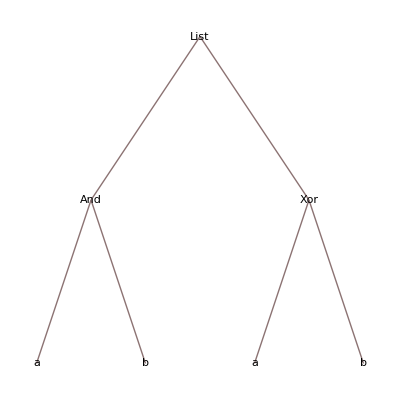

```mathematica
{And[a,b],Xor[a, b]} //TreeForm
```

### 2.3.2 Full Adder

A full adder is simply a bit wise addition machine with the ability to manage carry from lower bit, and forward its carry throught its output pin, carry. Therefore, it has one more input pin than half adder. It is called a full adder because it is usually made of two half adders. The truth table of a full adder can be shown below:

```mathematica
Grid[Insert[BooleanTable[{a, b,c, Or[And[a,b], And[b,c],And[a, c]], Xor[Xor[a, b],c]}, {a, b,c}] // Boole, {a, b, c,carry, sum}, 1], Spacings -> {2, 1}, Frame -> All, Background -> {{None, None, None,Gray}, {LightGray, None}}]
```

a | b | c | carry | sum
1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0

This is an interesting truth table, because one can think about the sum bit by using a two level Xor gate to ensure that only one of {a,b,c} pins is true, then the sum bit can be 1. The carry pin should be one when at least two of {a,b,c} are simultaneously 1s. That means we can use an Or gate to unite the three possible combinations of {a,b,c} pins being simultaneously turned on to be 1.

A more comprehensive solution can be displayed as follow:

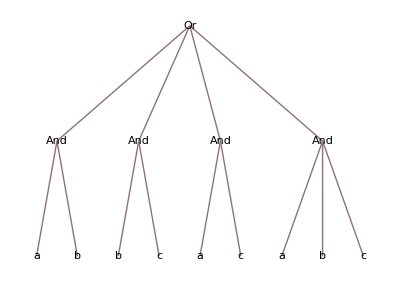

```mathematica
Or[And[a, b], And[b, c], And[a, c], And[a, b, c]] // TreeForm
```

Using the FullSimplify expression, we can see, the above expression can be automatically simplified to be the following:

```mathematica
Or[And[a, b], And[b, c], And[a, c], And[a, b, c]] // FullSimplify//FullForm
```

Or[And[a,Or[b,c]],And[b,c]]

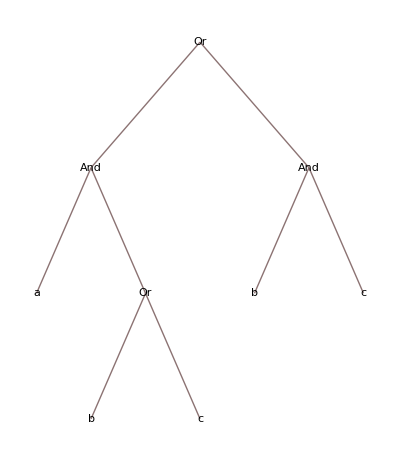

```mathematica
Or[And[a, b], And[b, c], And[a, c], And[a, b, c]] // FullSimplify // TreeForm
```

One may check its truth table, and find it consistent with the original expression. Note that this following function can be automatically proposed using Mathematica’s “suggstion” feature.

```mathematica
TableForm[BooleanTable[{a,b,c,(a&&(b||c))||(b&&c)},{a,b,c}]//Boole,TableHeadings->{None,{a,b,c,(a&&(b||c))||(b&&c)}}]
```

a | b | c | (a&&(b||c))||(b&&c)
1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 1 | 1 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0

## 2.3. The Arithmetic Logic Unit (ALU)

The design contract of ALU as specified by Nisan and Schocken, is simply a 15 bit adder with some other existing logical operations, such as negation (Not) or increment by one. The ALU takes only two 16 bit input channels, namely {x,y}. Then , the controlling bits, {zx, nx, zy, ny, f, no, out}, are just some slection bits to choose between different ways to perform simple operations. One may imagine, you can just use a number of multiplexers to redirect inputs to different logical operation circuits to get data processed. Then, after performing the logic operation, the ALU will also determine whether the output pins represents a number that is zero or not, indicated by the zr pin. If the output represent a negative number including the value zero, then, the ng pin will return 1. This roughly states the basic design contract of this ALU.

Given the specification, the suggested strategy to implement this chip, is to follow Figure 2.6 in the TECS book. First, use Mux16 to select whether one should negate or zero all bits from {x,y} input channels. Then, one may use the Add16 chip and And16 chip to perform instructions selected by the f pin. finally, one may implement the flipping of bits or not based on the values of no bit. It took me 18 chips to implement the whole ALU, and it should not be very difficult for people who carefully follow the book.

### 2.3.1 Caveats

Readers might run into some syntactical challenges when dealing with implementing ALU. The following syntax would be useful for implementation. First, individual pins of a multi-bit channel can be group selected using the array index syntax.

For example:

```mathematica
Or16(a=x, b=y, out[0..7]=lowerBits, out[8..15]=higherBits);
```

This syntax example shows that one can split the output into two sets of bits, and the HardwareSimulator would still work, and pipe the results to relevant pins as specified.

The other trick is to determine whether a number is negative or not. Using Or8Way chip, one may determine whether all the bits are zero or not. Then, it is easy to determine whether the represented number in its entirety is zero or not.

Reference for ALU implementation

Authorlast, “Article Title,” Journal Title, Volume(Issue), 2005 pp. #–#.

Authorlast1 and B. Authorlast2, “Article Title,” Journal Title, Volume(Issue), 2005 pp. #–#.

Authorlast1, B. Authorlast2, and C. Authorlast3, “Article Title,” Journal Title, Volume(Issue), 2005 pp. #–#.

Authorlast, Book Title, nth ed., Publisher Location: Publisher Name, 2005.

Authorlast1 and B. Authorlast2, Book Title, nth ed., Publisher Location: Publisher Name, 2005.

Authorlast1, B. Authorlast2, and C. Authorlast3, Book Title, nth ed., Publisher Location: Publisher Name, 2005.

Authorlast, “Paper Title,” in Conference Proceedings Title (Conference Acronym and Year), Conference Location (A. Authorlast, ed.), Publisher Location: Publisher Name, Publication Date pp. #–#.

Authorlast1, B. Authorlast2, and C. Authorlast3, “Paper Title,” in Conference Proceedings Title (Conference Acronym and Year), Conference Location (A. Authorlast, ed.), Publisher Location: Publisher Name, Publication Date pp. #–#.

Authorlast1, B. Authorlast2, and C. Authorlast3, “Paper Title,” in Conference Proceedings Title (Conference Acronym and Year), Conference Location (A. Authorlast, ed.), Publisher Location: Publisher Name, Publication Date pp. #–#.

Authorlast. “Website Title.” (Last updated date or date visited in three-character Month Day, Year format) URL.

B. Authorlast. “Entry Title” from CompanyN—A CompanyN Web Resource. URL.